## How to write math in the Mathematica

#### Mathematical Typesetting

To write equations in a text cell like this “∫_0^2 (x^2)dx”, you simply need to press [CTRL]+[9] (on mac or pc) and start typing, it’s kind of like inserting equations in text in a word document.
There are a few operations you can do by pressing [CTRL]+ another key.
Some examples are fractions ([CTRL]+[/]  → a/b), powers ([CTRL]+[^] → x^a), subscripts ([CTRL]+[_] →x_b ).
For special characters, you need the [ESC]-key. It will display a row of dots. then you can start typing commands (it will give you suggestions) 
Examples are uppercase and lowercase Greek letter (delta→ δ, Delta → Δ), integrals (int →∫ , dintt → ∫_□^□ □ⅆ□),  and many more. All of the operations also have a documentation page that you can look up.

#### Evaluating equations:

You can not only write, but of course also evaluate Math in the Wolfram Language.
Here are some examples of useful functions.

Put sums of fractions in terms of their lowest common denominator with Together:

```mathematica
Together[1/a+1/b]
```

(a+b)/(a b)

Factor a polynomial with Factor:

```mathematica
Factor[x^3-6x^2+11x-6]
```

(-3+x) (-2+x) (-1+x)

Guess what Expand does:

```mathematica
(*your code goes here*)
```

There is also a TrigExpand  that uses identities:

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

Use FullSimplify to simplify an expression (or check if there is a simplification you didn’t think of):

```mathematica
FullSimplify[2Log[2+2I]-Log[16I]]
```

-Log[2]

Solve a function or a set of functions using Solve.

```mathematica
Solve[x^2-8==0,x]
```

{{x→-2 √2},{x→2 √2}}

```mathematica
Solve[x^2+2y^3==3681 && x>0 && y>0,{x,y},Integers]
```

{{x→15,y→12},{x→41,y→10},{x→57,y→6}}

Take the derivative of a function

```mathematica
D[√(4 t^2+1),t]
```

(4 t)/(√(1+4 t^2))

Something else I find quite useful, is the fact that you can substitute any input in those functions: a variable to get a general form or numbers to get exact answers. Here is an example using Expectation which returns the expected value of an expression (e.g. x^2), under the assumption of a particular distribution (e.g. a NormalDistribution with mean μ and standard deviation σ)

If we give the function specific values for μ and σ, it also returns a numeric answer

```mathematica
Expectation[x^2,x\[Distributed]NormalDistribution[3,0.4]]
```

9.16

If we don’t specify σ, we can express the answer in terms of the standard deviation

```mathematica
Expectation[x^2,x\[Distributed]NormalDistribution[3,σ]]
```

9+σ^2

Same goes for the mean.

```mathematica
Expectation[x^2,x\[Distributed]NormalDistribution[μ,σ]]
```

μ^2+σ^2

So far we could have probably done this by hand, but if we add another variable n, we get a very complicated expression of the solution in terms of different distributions that would have been hard to find by hand.

```mathematica
Expectation[x^n,x\[Distributed]NormalDistribution[μ,σ]]
```

1/(√π)2^(-1+n/2) ((√2 μ (-(-σ)^n+σ^n) Gamma[1+n/2] Hypergeometric1F1[1/2-n/2,3/2,-μ^2/(2 σ^2)])/σ+((-σ)^n+σ^n) Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-μ^2/(2 σ^2)])

Of course there are many more functions to do math. Again, just look through the documentation for what you need.

#### Visualizations:

We saw how to graph functions or represent data in the last notebook using functions like Plot, ListPlot, or Plot3D.
Here are a few more functions:

RegionPlot shows the area of a plot that fulfills a certain criteria.
(&& means and)

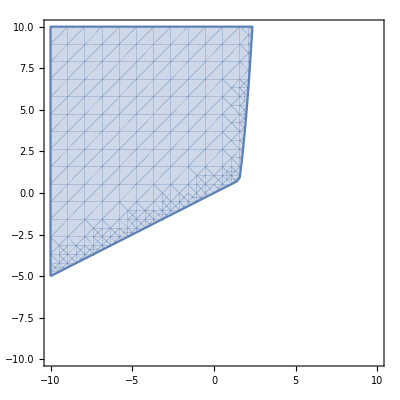

```mathematica
RegionPlot[{x^3-y<3&&x<2y},{x,-10,10},{y,-10,10}]
```

You should also become accustomed to a few options like adding PlotLegends or AxesLabel. In this case “Expressions” will automatically use the functions as names, you could also input a list of strings as for AxesLabel.

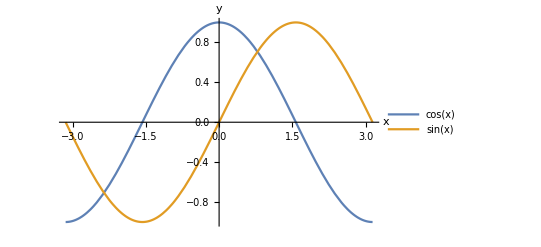

```mathematica
Plot[{Cos[x],Sin[x]},{x,-π,π},PlotLegends-> "Expressions",AxesLabel->{"x","y"}]
```

If you need a Logarithmic scale for an axis or both, simply use LogPlot or LogLogPlot.
Note: numbers like e ≈2.71828 or i= (√-1), are represented by capital letters.

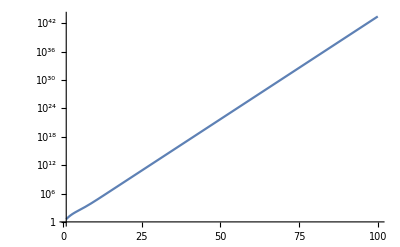

```mathematica
LogPlot[E^x+x^3, {x,1,100}]
```

#### Interactive notebooks:

A powerful tool for visualization are interactive functions.
If you take NS110U, you might recognize the function A*e^-βt cos(ωt-ϕ) that represents the behavior of a simple harmonic motion that oscillates. t represents time.
To better observe what each of the other factors do, you can use Manipulate. The syntax is similar to a plot whose variables you are increasing or decreasing in a certain range, but it allows you to have many more variables and adjust their values yourself.

```mathematica
Manipulate[Plot[A*Exp[-β*t]*Cos[ω*t-ϕ],{t,0,50},PlotRange->All, AxesLabel->{"t","x"}],{A ,0,10},{β,0,2},{ω,0,3},{ϕ,0,10}]
```

Manipulate doesn’t just work on graphics, you can also change parameters in functions:

```mathematica
Manipulate[Expand[(x+3)^n],{n,0,10,1}]
```

Or even options in a graph, such as color.

```mathematica
Manipulate[Plot3D[ Cos[a x]Sin[x y],{x,-3,3},{y,-3,3},PlotStyle->color,PerformanceGoal->"Quality"],{a,0.1,5},{color,{LightRed,LightBlue,LightGreen,Yellow}}]
```

#### A little cheat:

If you really don’t have an idea what function to use, try just creating a natural language field ([CTRL]+[=]) and searching for what you want to do:
-Graphics-
You will get a suggestion for a function, that you can modify and run:

```mathematica
LinguisticAssistant
```

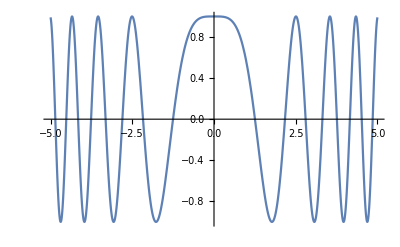

```mathematica
Plot[Cos[x^2], {x, -5, 5}]
```